```mathematica
Timing[
$HistoryLength=3;
ClearAll[XY,XZ,YZ];
clight=2.99792458*10^8;
(* Read in data file: put your directory path here *)
orb[1]=Import["/Users/stevenlund/studies/solenoid_nlo/numerical_check/sol_package/alldata_amp4e-2_velo0_kene4.823e5_sleng0.3_step6001.dat","Table"];

LENG[1]=Length[orb[1]];
X[1]=orb[1][[All,1]];
Vx[1]=orb[1][[All,2]];
Y[1]=orb[1][[All,3]];
Vy[1]=orb[1][[All,4]];
Z[1]=orb[1][[All,5]];
Vz[1]=orb[1][[All,6]];
XY[1]=orb[1][[All,{1,3}]];
Pthe[1]=orb[1][[All,{5,7}]];
RadKick[1]=orb[1][[All,{5,8}]];
RZ[1]=Table[{Z[1][[n]],(X[1][[n]]^2+Y[1][[n]]^2)^0.5},{n,1,LENG[1]}];
Beta3d[1]=Table[{Z[1][[n]],√(Vx[1][[n]]^2+Vy[1][[n]]^2+Vz[1][[n]]^2)/clight},{n,1,LENG[1]}];
Betaz[1]=Table[{Z[1][[n]],√(Vz[1][[n]]^2)/clight},{n,1,LENG[1]}];
Gamma3d[1]=Table[{Z[1][[n]],√(1/(1-((Vx[1][[n]]^2+Vy[1][[n]]^2+Vz[1][[n]]^2)/clight^2)))},{n,1,LENG[1]}];Gammaz[1]=Table[{Z[1][[n]],√(1/(1-((Vz[1][[n]]^2)/clight^2)))},{n,1,LENG[1]}];
]
```

{0.76422,Null}

```mathematica
(* Make plots of gamma and beta factors, both exact 3D and paraxial expanded form *)
```

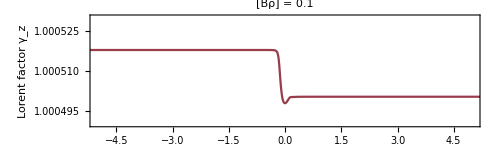

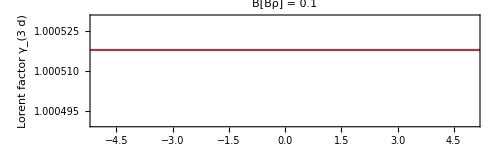

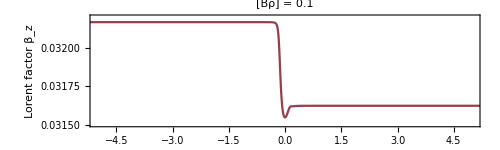

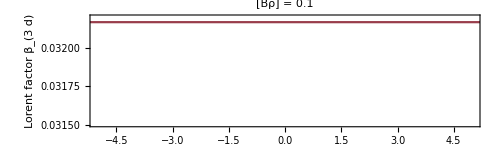

```mathematica
Gz[1]=ListPlot[Gammaz[1],PlotRange->{{-5,5},{1.00049,1.00053}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","Lorent factor γ_z"},LabelStyle->Directive[15],PlotLabel->Style["[Bρ] = 0.1",15],PlotStyle->ColorData[1,"ColorList"]]
G3d[1]=ListPlot[Gamma3d[1],PlotRange->{{-5,5},{1.00049,1.00053}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","Lorent factor γ_(3  d)"},LabelStyle->Directive[15],PlotLabel->Style["B[Bρ] = 0.1",15],PlotStyle->ColorData[1,"ColorList"]]
Bz[1]=ListPlot[Betaz[1],PlotRange->{{-5,5},{0.0315,0.0322}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","Lorent factor β_z"},LabelStyle->Directive[15],PlotLabel->Style["[Bρ] = 0.1",15],PlotStyle->ColorData[1,"ColorList"]]
B3d[1]=ListPlot[Beta3d[1],PlotRange->{{-5,5},{0.0315,0.0322}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","Lorent factor β_(3  d)"},LabelStyle->Directive[15],PlotLabel->Style["[Bρ] = 0.1",15],PlotStyle->ColorData[1,"ColorList"]]
```

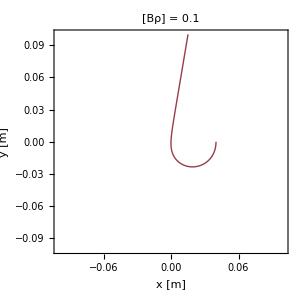

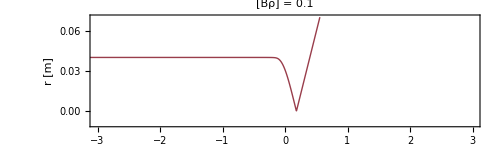

```mathematica
(* Make sample orbit plot: both x-y and r-z *)
Xy[1]=ListPlot[XY[1],PlotRange->{{-0.1,0.1},{-0.1,0.1}},AspectRatio->1,ImageSize->{300,300},Axes->None,Joined->True,Frame->True,FrameLabel->{"x [m]","y [m]"},LabelStyle->Directive[18],PlotLabel->Style["[Bρ] = 0.1",18],PlotStyle->ColorData[1,"ColorList"]]

Rz[1]=ListPlot[RZ[1],PlotRange->{{-3,3},{-0.01,0.07}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","r [m]"},LabelStyle->Directive[14],PlotLabel->Style["[Bρ] = 0.1",15],PlotStyle->ColorData[1,"ColorList"]]
```

```mathematica
(* Plot canonical angular momentum and the integrand argument for the r' kick *)
```

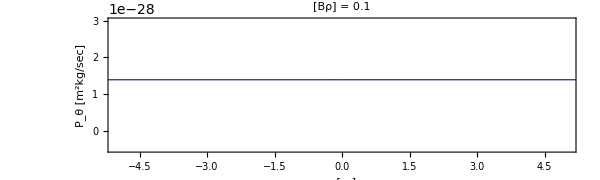

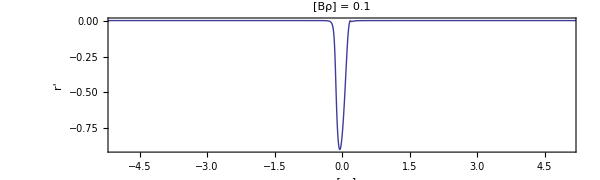

```mathematica
PThe[1]=ListPlot[Pthe[1],PlotRange->{{-5,5},{-0.5*10^-28,3*10^-28}},Axes->None,AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ [m^2kg/sec]"},LabelStyle->Directive[11],ImageSize->{600,180},PlotLabel->Style["[Bρ] = 0.1",15]]
ToRK[1]=ListPlot[RadKick[1],PlotRange->{{-5,5},All},Axes->None,AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","r'"},LabelStyle->Directive[13],ImageSize->{600,180},PlotLabel->Style["[Bρ] = 0.1",15]]
```